```mathematica
(* Analytical Integrations of the B->V Rates*)
```

```mathematica
(* Base definition of the rate *)
```

```mathematica
(* Reference for the implementation: https://arxiv.org/pdf/1702.01521.pdf *)
(* No explicit implementation for the helicity amplitudes required *)
```

```mathematica
(* Zero Lepton Mass Approximation *)
```

```mathematica
Γ[w_, cosL_, cosV_, chi_]:=Subscript[N, 0] f[w]  * (
(1-cosL)^2sinV^2  SubPlus[H][w]^2 + (1+cosL)^2sinV^2 SubMinus[H] [w]^2
+ 4sinL^2cosV^2 Subscript[H, 0][w]^2 - 2sinL^2sinV^2Cos[2chi]SubPlus[H][w]SubMinus[H][w]
- 4sinL(1-cosL)sinV cosV Cos[chi]SubPlus[H][w]Subscript[H, 0][w]
+ 4sinL(1+cosL)sinV cosV Cos[chi]SubMinus[H][w]Subscript[H, 0][w]
)/.sinL->Sqrt[1-cosL^2]/.sinV->Sqrt[1-cosV^2]
```

```mathematica
Simplify[Γ[w, cosL, cosV, chi]]
```

f[w] N_0 (-(1+cosL)^2 (-1+cosV^2) (H_-[w])^2-2 (-1+cosL^2) (-1+cosV^2) Cos[2 chi] H_-[w] H_+[w]-(-1+cosL)^2 (-1+cosV^2) (H_+[w])^2+4 (1+cosL) √(1-cosL^2) cosV √(1-cosV^2) Cos[chi] H_-[w] H_0[w]+4 (-1+cosL) √(1-cosL^2) cosV √(1-cosV^2) Cos[chi] H_+[w] H_0[w]-4 (-1+cosL^2) cosV^2 H_0[w]^2)

```mathematica
(* Full Lepton Mass Effects *)
```

```mathematica
(* pm = +/- *)
(* (6 Subscript[m, B] Subscript[m, V]^2/8/(4π)^2 Subscript[G, F]^2 Subscript[η, EW]^2BR)->Subscript[N, 0] *)
(*f[w_]:=Sqrt[w^2-1](1-2w r + r^2);*)
```

```mathematica
λ[q2]:=((Subscript[m, B]^2 + Subscript[m, V]^2)^2 -q2)((Subscript[m, B]^2 - Subscript[m, V]^2)^2 -q2)
```

```mathematica
Subscript[Γ, full][w_, cosL_, cosV_, chi_]:=Subscript[N, 0]/(6 Subscript[m, B] Subscript[m, V]^2/8)Abs[Subscript[V, cb]]^2 (q2 - Subscript[m, l]^2)^2/12/Subscript[m, B]^2/q2  pD(
3/8 (1+cosL^2) 3/4 sinV^2(SubPlus[H][w]^2+SubMinus[H][w])^2
+3/4 sinL^2 3/2 cosV^2 Subscript[H, 0][w]^2
-3/4sinL^2 Cos[2chi] 3/4 sinV^2 SubPlus[H][w]SubMinus[H][w]
-9/32 sin2L Cos[chi] sin2V (SubPlus[H][w]Subscript[H, 0][w]+SubMinus[H][w]Subscript[H, 0][w])
+pm 3/4cosL 3/4sinV^2 (SubPlus[H][w]^2-SubMinus[H][w]^2)
-pm 9/16 sinL cos[chi] sin2V (SubPlus[H][w]Subscript[H, 0][w]-SubMinus[H][w]Subscript[H, 0][w])
+3/4 sinL^2 3/4 sinV^2 Subscript[m, l]/2/q2(SubPlus[H][w]^2+SubMinus[H][w])^2
+3/2 cosL^2 3/2 cosV^2 Subscript[m, l]/2/q2 Subscript[H, 0][w]^2
+3/4 sinL^2 Cos[2chi] 3/4 sinV^2 Subscript[m, l]^2/2/q2  SubPlus[H][w]SubMinus[H][w]
+9/16 sin2L Cos[chi] sin2V Subscript[m, l]^2/2/q2 (SubPlus[H][w]Subscript[H, 0][w]+SubMinus[H][w]Subscript[H, 0][w])
+9/2 cosV^2 1/2 Subscript[m, l]^2/2/q2 Subscript[H, s][w]^2
+3 cosL 3/2 cosV^2 Subscript[m, l]^2/2/q2 Subscript[H, s][w]Subscript[H, 0][w]
+9/8 sinL Cos[chi] sin2V Subscript[m, l]^2/2/q2 (SubPlus[H][w]Subscript[H, s][w] + SubMinus[H][w]Subscript[H, s][w])
)/.sin2L->2sinL cosL/.sin2V->2sinV cosV/.sinL->Sqrt[1-cosL^2]/.sinV->Sqrt[1-cosV^2]/.pD->Subscript[m, V] Sqrt[w^2-1]/.q2->Subscript[m, B]^2 + Subscript[m, V]^2 -2 Subscript[m, B] Subscript[m, V] w/.pm->1
```

```mathematica
Simplify[Subscript[Γ, full][w, cosL, cosV, chi]/.Subscript[m, l]->0]
```

1/(32 m_B^3 m_V)√(-1+w^2) Abs[V_cb]^2 (-m_B^2+2 w m_B m_V-m_V^2) N_0 ((-1+cosL)^2 (-1+cosV^2) (H_-[w])^2+2 cosL (-1+cosV^2) (H_+[w])^2+(1+cosL^2) (-1+cosV^2) (H_+[w])^4+4 √(1-cosL^2) cosV √(1-cosV^2) (cos[chi]+cosL Cos[chi]) H_+[w] H_0[w]+4 (-1+cosL^2) cosV^2 H_0[w]^2+2 H_-[w] ((-1+cosL^2) (-1+cosV^2) Cos[2 chi] H_+[w]+(1+cosL^2) (-1+cosV^2) (H_+[w])^2+2 √(1-cosL^2) cosV √(1-cosV^2) (-cos[chi]+cosL Cos[chi]) H_0[w]))

```mathematica
(* Define what we want to use in the following *)
```

```mathematica
(*Γ[w_,cosL_,cosV_,chi_]:=Γ[w,cosL,cosV,chi]*)
```

```mathematica
(* Integration of one variable *)
```

```mathematica
(* cosL *)
```

```mathematica
ΓcosLIntegrated[w_,cosV_,chi_,cosLmin_,cosLmax_]:=Evaluate[Integrate[Γ[w, cosL, cosV,chi],{cosL, cosLmin,cosLmax}, 
Assumptions ->{Element[cosLmin,Reals], Element[cosLmax,Reals],-1<cosLmin<1,-1<cosLmax<1,cosLmin !=cosLmax }
]]
```

```mathematica
ΓcosLIntegrated[w,cosV,chi,cosLmin,cosLmax]
```

1/3 f[w] N_0 (-3 (cosLmax+cosLmax^2+cosLmax^3/3-1/3 cosLmin (3+cosLmin (3+cosLmin))) (-1+cosV^2) (H_-[w])^2-2 (-3 cosLmax+cosLmax^3+3 cosLmin-cosLmin^3) (-1+cosV^2) Cos[2 chi] H_-[w] H_+[w]-(cosLmax-cosLmin) (3+cosLmax^2+cosLmax (-3+cosLmin)+(-3+cosLmin) cosLmin) (-1+cosV^2) (H_+[w])^2+2 cosV √(1-cosV^2) (-2 √(1-cosLmax^2)+cosLmax (3+2 cosLmax) √(1-cosLmax^2)+2 √(1-cosLmin^2)-cosLmin (3+2 cosLmin) √(1-cosLmin^2)+3 ArcSin[cosLmax]-3 ArcSin[cosLmin]) Cos[chi] H_-[w] H_0[w]+2 cosV √(1-cosV^2) (-2 √(1-cosLmax^2)+cosLmax (-3+2 cosLmax) √(1-cosLmax^2)+2 √(1-cosLmin^2)+(3-2 cosLmin) cosLmin √(1-cosLmin^2)-3 ArcSin[cosLmax]+3 ArcSin[cosLmin]) Cos[chi] H_+[w] H_0[w]-4 (-3 cosLmax+cosLmax^3+3 cosLmin-cosLmin^3) cosV^2 H_0[w]^2)

```mathematica
ΓcosLIntegrated[w,cosV,chi,-1,1]
```

1/3 f[w] N_0 (-8 (-1+cosV^2) (H_-[w])^2+8 (-1+cosV^2) Cos[2 chi] H_-[w] H_+[w]-8 (-1+cosV^2) (H_+[w])^2+6 cosV √(1-cosV^2) π Cos[chi] H_-[w] H_0[w]-6 cosV √(1-cosV^2) π Cos[chi] H_+[w] H_0[w]+16 cosV^2 H_0[w]^2)

```mathematica
(* cosV *)
```

```mathematica
ΓcosVIntegrated[w_,cosL_,chi_,cosVmin_,cosVmax_]:=Evaluate[Integrate[Γ[w, cosL, cosV,chi],{cosV, cosVmin,cosVmax}, 
Assumptions ->{Element[cosVmin,Reals], Element[cosVmax,Reals],-1<cosVmin<1,-1<cosVmax<1,cosVmin !=cosVmax }
]]
```

```mathematica
ΓcosVIntegrated[w,cosL,chi,cosVmin,cosVmax]
```

1/3 f[w] N_0 (-(1+cosL)^2 (-3 cosVmax+cosVmax^3+3 cosVmin-cosVmin^3) (H_-[w])^2-2 (-1+cosL^2) (-3 cosVmax+cosVmax^3+3 cosVmin-cosVmin^3) Cos[2 chi] H_-[w] H_+[w]-(-1+cosL)^2 (-3 cosVmax+cosVmax^3+3 cosVmin-cosVmin^3) (H_+[w])^2+4 (1+cosL) √(1-cosL^2) (-√(1-cosVmax^2)+cosVmax^2 √(1-cosVmax^2)+√(1-cosVmin^2)-cosVmin^2 √(1-cosVmin^2)) Cos[chi] H_-[w] H_0[w]+4 (-1+cosL) √(1-cosL^2) (-√(1-cosVmax^2)+cosVmax^2 √(1-cosVmax^2)+√(1-cosVmin^2)-cosVmin^2 √(1-cosVmin^2)) Cos[chi] H_+[w] H_0[w]-4 (-1+cosL^2) (cosVmax^3-cosVmin^3) H_0[w]^2)

```mathematica
ΓcosVIntegrated[w,cosL,chi,-1,1]
```

1/3 f[w] N_0 (4 (1+cosL)^2 (H_-[w])^2+8 (-1+cosL^2) Cos[2 chi] H_-[w] H_+[w]+4 (-1+cosL)^2 (H_+[w])^2-8 (-1+cosL^2) H_0[w]^2)

```mathematica
(* chi *)
```

```mathematica
ΓchiIntegrated[w_,cosL_,cosV_,chimin_,chimax_]:=Evaluate[Integrate[Γ[w, cosL, cosV,chi],{chi, chimin,chimax}, 
Assumptions ->{Element[chimin,Reals], Element[chimax,Reals],0<chimin<2π,0<chimax<2π,chimin !=chimax }
]]
```

```mathematica
ΓchiIntegrated[w,cosL,cosV,chimin,chimax]
```

f[w] N_0 (-((chimax-chimin) (1+cosL)^2 (-1+cosV^2) (H_-[w])^2)-(-1+cosL^2) (-1+cosV^2) (Sin[2 chimax]-Sin[2 chimin]) H_-[w] H_+[w]-(chimax-chimin) (-1+cosL)^2 (-1+cosV^2) (H_+[w])^2+4 (1+cosL) √(1-cosL^2) cosV √(1-cosV^2) (Sin[chimax]-Sin[chimin]) H_-[w] H_0[w]+4 (-1+cosL) √(1-cosL^2) cosV √(1-cosV^2) (Sin[chimax]-Sin[chimin]) H_+[w] H_0[w]-4 (chimax-chimin) (-1+cosL^2) cosV^2 H_0[w]^2)

```mathematica
ΓchiIntegrated[w,cosL,cosV,0,2π]
```

f[w] N_0 (-2 (1+cosL)^2 (-1+cosV^2) π (H_-[w])^2-2 (-1+cosL)^2 (-1+cosV^2) π (H_+[w])^2-8 (-1+cosL^2) cosV^2 π H_0[w]^2)

```mathematica
(* Integration of two variables *)
```

```mathematica
(* cosL cosV *)
```

```mathematica
ΓcosLcosVIntegrated[w_,chi_,cosLmin_,cosLmax_,cosVmin_,cosVmax_]:=Evaluate[Integrate[Γ[w, cosL, cosV,chi],{cosL, cosLmin,cosLmax}, {cosV, cosVmin,cosVmax}, 
Assumptions ->{
Element[cosLmin,Reals], Element[cosLmax,Reals],-1<cosLmin<1,-1<cosLmax<1,cosLmin !=cosLmax ,
Element[cosVmin,Reals], Element[cosVmax,Reals],-1<cosVmin<1,-1<cosVmax<1,cosVmin !=cosVmax 
}
]]
```

```mathematica
ΓcosLcosVIntegrated[w, chi,cosLmin, cosLmax, cosVmin, cosVmax]
```

1/9 f[w] N_0 (-3 (cosLmax+cosLmax^2+cosLmax^3/3-1/3 cosLmin (3+cosLmin (3+cosLmin))) (-3 cosVmax+cosVmax^3+3 cosVmin-cosVmin^3) (H_-[w])^2-2 (-3 cosLmax+cosLmax^3+3 cosLmin-cosLmin^3) (-3 cosVmax+cosVmax^3+3 cosVmin-cosVmin^3) Cos[2 chi] H_-[w] H_+[w]-(cosLmax-cosLmin) (3+cosLmax^2+cosLmax (-3+cosLmin)+(-3+cosLmin) cosLmin) (-3 cosVmax+cosVmax^3+3 cosVmin-cosVmin^3) (H_+[w])^2+2 (-(1-cosVmax^2)^(3/2)+(1-cosVmin^2)^(3/2)) (-2 √(1-cosLmax^2)+cosLmax (3+2 cosLmax) √(1-cosLmax^2)+2 √(1-cosLmin^2)-cosLmin (3+2 cosLmin) √(1-cosLmin^2)+3 ArcSin[cosLmax]-3 ArcSin[cosLmin]) Cos[chi] H_-[w] H_0[w]+2 (-(1-cosVmax^2)^(3/2)+(1-cosVmin^2)^(3/2)) (-2 √(1-cosLmax^2)+cosLmax (-3+2 cosLmax) √(1-cosLmax^2)+2 √(1-cosLmin^2)+(3-2 cosLmin) cosLmin √(1-cosLmin^2)-3 ArcSin[cosLmax]+3 ArcSin[cosLmin]) Cos[chi] H_+[w] H_0[w]-4 (-3 cosLmax+cosLmax^3+3 cosLmin-cosLmin^3) (cosVmax^3-cosVmin^3) H_0[w]^2)

```mathematica
ΓcosLcosVIntegrated[w, chi,-1, 1, -1, 1]
```

1/9 f[w] N_0 (32 (H_-[w])^2-32 Cos[2 chi] H_-[w] H_+[w]+32 (H_+[w])^2+32 H_0[w]^2)

```mathematica
(* cosL chi *)
```

```mathematica
ΓcosLchiIntegrated[w_,cosV_,cosLmin_,cosLmax_,chimin_,chimax_]:=Evaluate[Integrate[Γ[w, cosL, cosV,chi],{cosL, cosLmin,cosLmax}, {chi, chimin,chimax}, 
Assumptions ->{
Element[cosLmin,Reals], Element[cosLmax,Reals],-1<cosLmin<1,-1<cosLmax<1,cosLmin !=cosLmax ,
Element[chimin,Reals], Element[chimax,Reals],0<chimin<2π,0<chimax<2π,chimin !=chimax 
}
]]
```

```mathematica
ΓcosLchiIntegrated[w,cosV,cosLmin,cosLmax,chimin,chimax]
```

1/3 f[w] N_0 (-3 (chimax-chimin) (cosLmax+cosLmax^2+cosLmax^3/3-1/3 cosLmin (3+cosLmin (3+cosLmin))) (-1+cosV^2) (H_-[w])^2-(chimax-chimin) (cosLmax-cosLmin) (3+cosLmax^2+cosLmax (-3+cosLmin)+(-3+cosLmin) cosLmin) (-1+cosV^2) (H_+[w])^2+2 cosV √(1-cosV^2) (-2 √(1-cosLmax^2)+cosLmax (-3+2 cosLmax) √(1-cosLmax^2)+2 √(1-cosLmin^2)+(3-2 cosLmin) cosLmin √(1-cosLmin^2)-3 ArcSin[cosLmax]+3 ArcSin[cosLmin]) (Sin[chimax]-Sin[chimin]) H_+[w] H_0[w]-4 (chimax-chimin) (-3 cosLmax+cosLmax^3+3 cosLmin-cosLmin^3) cosV^2 H_0[w]^2-2 Sin[(chimax-chimin)/2] H_-[w] ((-3 cosLmax+cosLmax^3+3 cosLmin-cosLmin^3) (-1+cosV^2) (Cos[1/2 (3 chimax+chimin)]+Cos[1/2 (chimax+3 chimin)]) H_+[w]-2 cosV √(1-cosV^2) (-2 √(1-cosLmax^2)+3 cosLmax √(1-cosLmax^2)+2 cosLmax^2 √(1-cosLmax^2)+2 √(1-cosLmin^2)-3 cosLmin √(1-cosLmin^2)-2 cosLmin^2 √(1-cosLmin^2)+3 ArcSin[cosLmax]-3 ArcSin[cosLmin]) Cos[(chimax+chimin)/2] H_0[w]))

```mathematica
ΓcosLchiIntegrated[w,cosV,-1,1,0,2π]
```

1/3 f[w] N_0 (-16 (-1+cosV^2) π (H_-[w])^2-16 (-1+cosV^2) π (H_+[w])^2+32 cosV^2 π H_0[w]^2)

```mathematica
(* cosV chi *)
```

```mathematica
ΓcosVchiIntegrated[w_,cosL_,cosVmin_,cosVmax_,chimin_,chimax_]:=Evaluate[Integrate[Γ[w, cosL, cosV,chi],{cosV, cosVmin,cosVmax}, {chi, chimin,chimax}, 
Assumptions ->{
Element[cosVmin,Reals], Element[cosVmax,Reals],-1<cosVmin<1,-1<cosVmax<1,cosVmin !=cosVmax ,
Element[chimin,Reals], Element[chimax,Reals],0<chimin<2π,0<chimax<2π,chimin !=chimax 
}
]]
```

```mathematica
ΓcosVchiIntegrated[w,cosL,cosVmin,cosVmax,chimin,chimax]
```

1/3 f[w] N_0 (-((chimax-chimin) (1+cosL)^2 (-3 cosVmax+cosVmax^3+3 cosVmin-cosVmin^3) (H_-[w])^2)-(chimax-chimin) (-1+cosL)^2 (-3 cosVmax+cosVmax^3+3 cosVmin-cosVmin^3) (H_+[w])^2+4 (-1+cosL) √(1-cosL^2) (-√(1-cosVmax^2)+cosVmax^2 √(1-cosVmax^2)+√(1-cosVmin^2)-cosVmin^2 √(1-cosVmin^2)) (Sin[chimax]-Sin[chimin]) H_+[w] H_0[w]-4 (chimax-chimin) (-1+cosL^2) (cosVmax^3-cosVmin^3) H_0[w]^2-(1+cosL) H_-[w] ((-1+cosL) (-3 cosVmax+cosVmax^3+3 cosVmin-cosVmin^3) (Sin[2 chimax]-Sin[2 chimin]) H_+[w]-4 √(1-cosL^2) (-√(1-cosVmax^2)+cosVmax^2 √(1-cosVmax^2)+√(1-cosVmin^2)-cosVmin^2 √(1-cosVmin^2)) (Sin[chimax]-Sin[chimin]) H_0[w]))

```mathematica
ΓcosVchiIntegrated[w,cosL,-1,1,0,2π]
```

1/3 f[w] N_0 (8 (1+cosL)^2 π (H_-[w])^2+8 (-1+cosL)^2 π (H_+[w])^2-16 (-1+cosL^2) π H_0[w]^2)

```mathematica
(* Integration of three variables *)
```

```mathematica
(* cosL cosV chi *)
```

```mathematica
ΓcosLcosVchiIntegrated[w_,cosLmin_, cosLmax_,cosVmin_,cosVmax_,chimin_,chimax_]:=Evaluate[Integrate[Γ[w, cosL, cosV,chi],{cosL, cosLmin,cosLmax},{cosV, cosVmin,cosVmax}, {chi, chimin,chimax}, 
Assumptions ->{
Element[cosLmin,Reals], Element[cosLmax,Reals],-1<cosLmin<1,-1<cosLmax<1,cosLmin<cosLmax, cosLmin !=cosLmax ,
Element[cosVmin,Reals], Element[cosVmax,Reals],-1<cosVmin<1,-1<cosVmax<1,cosVmin<cosVmax,cosVmin !=cosVmax ,
Element[chimin,Reals], Element[chimax,Reals],0<chimin<2π,0<chimax<2π,chimin<chimax,chimin !=chimax 
}
]]
```

```mathematica
ΓcosLcosVchiIntegrated[w,cosLmin, cosLmax,cosVmin,cosVmax,chimin,chimax]
```

1/3 f[w] N_0 (-((chimax-chimin) (cosLmax+cosLmax^2+cosLmax^3/3-1/3 cosLmin (3+cosLmin (3+cosLmin))) (-3 cosVmax+cosVmax^3+3 cosVmin-cosVmin^3) (H_-[w])^2)-1/3 (-3 cosLmax+cosLmax^3+3 cosLmin-cosLmin^3) (-3 cosVmax+cosVmax^3+3 cosVmin-cosVmin^3) (Sin[2 chimax]-Sin[2 chimin]) H_-[w] H_+[w]-1/3 (chimax-chimin) (cosLmax-cosLmin) (3+cosLmax^2+cosLmax (-3+cosLmin)+(-3+cosLmin) cosLmin) (-3 cosVmax+cosVmax^3+3 cosVmin-cosVmin^3) (H_+[w])^2+2/3 (-√(1-cosVmax^2)+cosVmax^2 √(1-cosVmax^2)+√(1-cosVmin^2)-cosVmin^2 √(1-cosVmin^2)) (-2 √(1-cosLmax^2)+3 cosLmax √(1-cosLmax^2)+2 cosLmax^2 √(1-cosLmax^2)+2 √(1-cosLmin^2)-3 cosLmin √(1-cosLmin^2)-2 cosLmin^2 √(1-cosLmin^2)+3 ArcSin[cosLmax]-3 ArcSin[cosLmin]) (Sin[chimax]-Sin[chimin]) H_-[w] H_0[w]+2/3 (-√(1-cosVmax^2)+cosVmax^2 √(1-cosVmax^2)+√(1-cosVmin^2)-cosVmin^2 √(1-cosVmin^2)) (-2 √(1-cosLmax^2)-3 cosLmax √(1-cosLmax^2)+2 cosLmax^2 √(1-cosLmax^2)+2 √(1-cosLmin^2)+3 cosLmin √(1-cosLmin^2)-2 cosLmin^2 √(1-cosLmin^2)-3 ArcSin[cosLmax]+3 ArcSin[cosLmin]) (Sin[chimax]-Sin[chimin]) H_+[w] H_0[w]-4/3 (chimax-chimin) (-3 cosLmax+cosLmax^3+3 cosLmin-cosLmin^3) (cosVmax^3-cosVmin^3) H_0[w]^2)

```mathematica
ΓcosLcosVchiIntegrated[w,-1, 1,-1,1,0,2π]
```

1/3 f[w] N_0 (64/3 π (H_-[w])^2+64/3 π (H_+[w])^2+64/3 π H_0[w]^2)

```mathematica
(* Define CLN parametrization *)
```

```mathematica
wmin=1;
wmax=(Subscript[m, B]^2 + Subscript[m, V]^2) / (2 Subscript[m, B] Subscript[m, V]);
```

```mathematica
(* Define form factors and helicity amplitudes in a generic way *)
```

```mathematica
rprime=2Sqrt[Subscript[m, B] Subscript[m, V]]/(Subscript[m, B]+Subscript[m, V]);
```

```mathematica
Subscript[A, 1][w_]:=(w+1)/2 rprime Subscript[h, A1][w]
```

```mathematica
Subscript[A, 2][w_]:=Subscript[R, 2][w]/rprime Subscript[h, A1][w]
```

```mathematica
V[w_]:=Subscript[R, 1][w]/rprime Subscript[h, A1][w]
```

```mathematica
SubPlus[H][w_]:=(Subscript[m, B]+Subscript[m, V])Subscript[A, 1][w]-2 Subscript[m, B]/(Subscript[m, B]+Subscript[m, V])Subscript[m, V] Sqrt[w^2-1]V[w]
```

```mathematica
SubMinus[H][w_]:=(Subscript[m, B]+Subscript[m, V])Subscript[A, 1][w]+2 Subscript[m, B]/(Subscript[m, B]+Subscript[m, V])Subscript[m, V] Sqrt[w^2-1]V[w]
```

```mathematica
Subscript[H, 0][w_]:=1/(2 Subscript[m, V] Sqrt[q2])((Subscript[m, B]^2-Subscript[m, V]^2-q2)(Subscript[m, B]+Subscript[m, V])Subscript[A, 1][w]-4 Subscript[m, B]^2 Subscript[m, V]^2(w^2-1)/(Subscript[m, B]+Subscript[m, V])Subscript[A, 2][w])/.q2->Subscript[m, B]^2+Subscript[m, V]^2-2w Subscript[m, B] Subscript[m, V]
```

```mathematica
(* Define CLN form factors *)
```

```mathematica
z[w_]:=(Sqrt[w+1] - Sqrt[2]) / (Sqrt[w+1] + Sqrt[2])
(* https://arxiv.org/abs/1702.01521v2 *)
hA11=0.906;
rho2=1.03;
R11=1.38;
R21=0.97;
```

```mathematica
(*Masses and other things *)
Subscript[N, 0]= 6 Subscript[m, B] Subscript[m, V]^2 / 8 / (4π)^4 Subscript[G, F]^2 Abs[Subscript[V, cb]]^2 Subscript[η, EW] ^2BrDst;
f[w_]:=Sqrt[w^2-1](1-2w r + r^2);
Subscript[m, B]=5.27963;
Subscript[m, V]=2.01026;
Subscript[m, l]=0;
r=Subscript[m, V]/Subscript[m, B];
Subscript[V, cb]=40*10^-3;
Subscript[G, F]=1.1663787*10^-5;
Subscript[η, EW]=1.0066;
BrDst=1;
```

```mathematica
Subscript[h, A1][w_]:=hA11(1-8rho2 z[w]+(53*rho2-15)z[w]^2-(231rho2-91)z[w]^3)
```

```mathematica
Subscript[R, 1][w_]:=R11-0.12(w-1)+0.05(w-1)^2
```

```mathematica
Subscript[R, 2][w_]:=R21+0.11(w-1)-0.06(w-1)^2
```

```mathematica
(* 1D Plots *)
```

```mathematica
dΓdw[w_]:=ΓcosLcosVchiIntegrated[w,-1, 1,-1,1,0,2π]
```

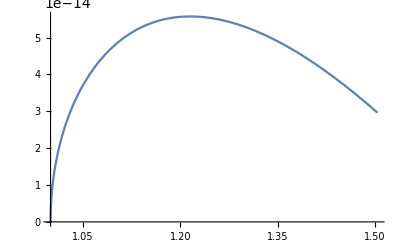

```mathematica
Plot[dΓdw[w],{w,wmin, wmax}]
```

```mathematica
dΓdcosL[cosL_]:=NIntegrate[ΓcosVchiIntegrated[w,cosL,-1,1,0,2π],{w, wmin, wmax}]
```

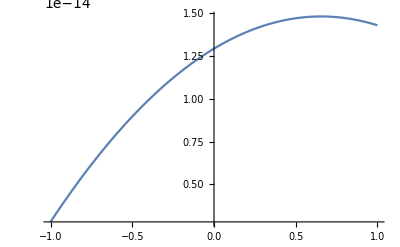

```mathematica
Plot[dΓdcosL[cosL],{cosL, -1, 1}]
```

```mathematica
dΓdcosV[cosV_]:=NIntegrate[ΓcosLchiIntegrated[w,cosV,-1,1,0,2π],{w,wmin,wmax}]
```

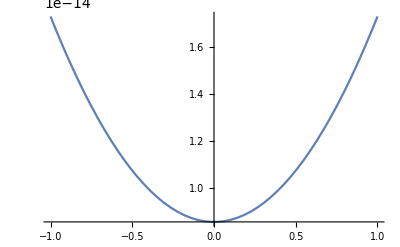

```mathematica
Plot[dΓdcosV[cosV],{cosV,-1,1}]
```

```mathematica
dΓdchi[chi_]:=NIntegrate[ΓcosLcosVIntegrated[w,chi,-1,1,-1, 1],{w,wmin,wmax}]
```

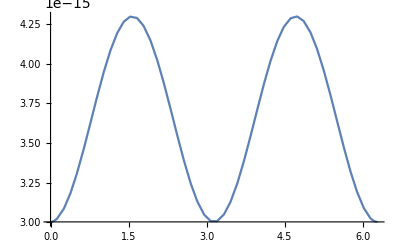

```mathematica
Plot[dΓdchi[chi],{chi,0,2π}]
```

```mathematica
(* 2D Plots *)
```

```mathematica
dΓdwcosL[w_,cosL_]:=ΓcosVchiIntegrated[w,cosL,-1,1,0,2π]
dΓdwcosLProduct[w_,cosL_]:=dΓdw[w]dΓdcosL[cosL]*10^15
```

```mathematica
dΓdwcosLProduct[1.2, 0.2]
```

7.73145×10^-13

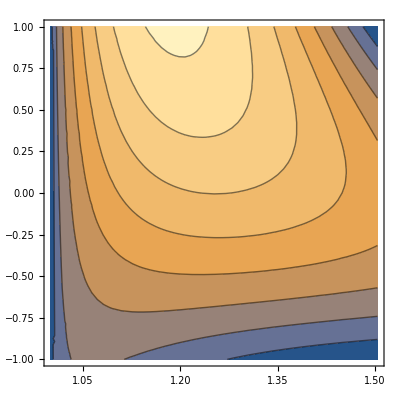

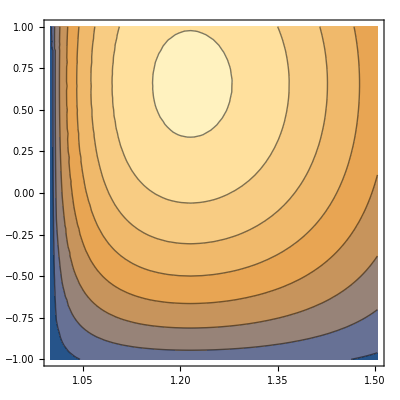

```mathematica
ContourPlot[dΓdwcosL[w, cosL],{w,wmin,wmax},{cosL, -1, 1}]
ContourPlot[dΓdwcosLProduct[w, cosL],{w,wmin,wmax},{cosL, -1, 1}]
```

```mathematica
dΓdwcosV[w_,cosV_]:=ΓcosLchiIntegrated[w,cosV,-1,1,0,2π]
dΓdwcosVProduct[w_,cosV_]:=dΓdw[w]dΓdcosV[cosV]*10^15
```

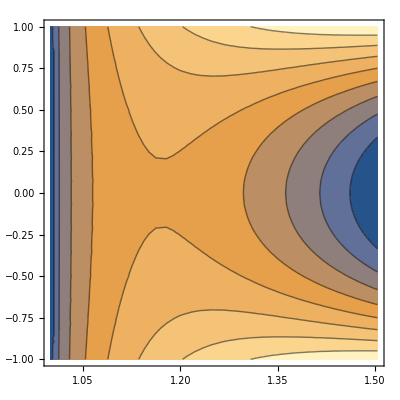

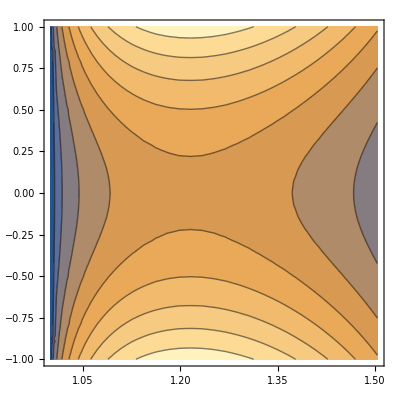

```mathematica
ContourPlot[dΓdwcosV[w, cosV],{w,wmin,wmax},{cosV, -1, 1}]
ContourPlot[dΓdwcosVProduct[w, cosV],{w,wmin,wmax},{cosV, -1, 1}]
```

```mathematica
dΓdwchi[w_,chi_]:=ΓcosLcosVIntegrated[w,chi,-1,1,-1,1]
dΓdwchiProduct[w_,chi_]:=dΓdw[w]dΓdchi[chi]*10^15
```

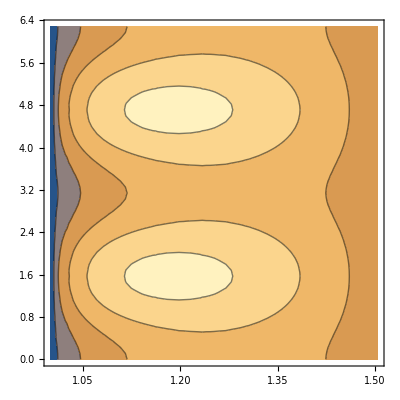

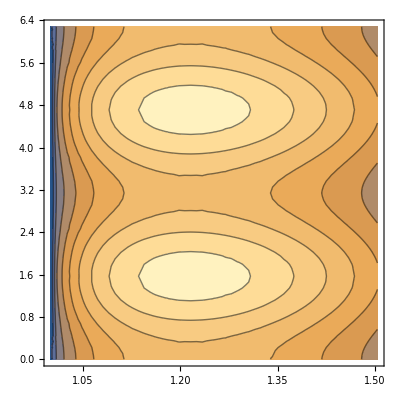

```mathematica
ContourPlot[dΓdwchi[w, chi],{w,wmin,wmax},{chi, 0, 2π}]
ContourPlot[dΓdwchiProduct[w, chi],{w,wmin,wmax},{chi, 0, 2π}]
```

```mathematica
dΓdcosLdcosV[cosL_,cosV_]:=NIntegrate[ΓchiIntegrated[w,cosL,cosV,0,2π],{w,wmin,wmax}]
dΓdcosLdcosVProduct[cosL_,cosV_]:=dΓdcosL[cosL]dΓdcosV[cosV]*10^15
```

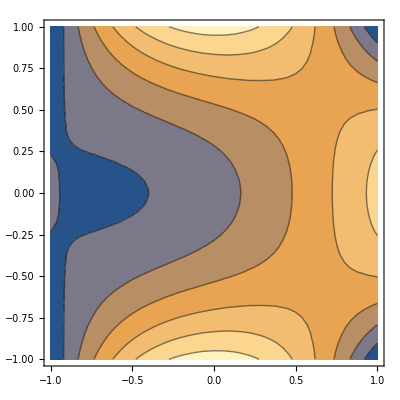

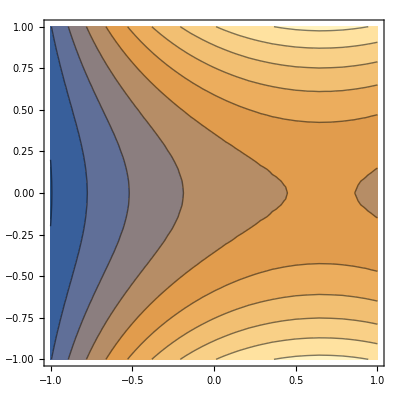

```mathematica
ContourPlot[dΓdcosLdcosV[cosL,cosV],{cosL, -1, 1},{cosV, -1, 1}]
ContourPlot[dΓdcosLdcosVProduct[cosL,cosV],{cosL, -1, 1},{cosV, -1, 1}]
```

```mathematica
dΓdcosLdchi[cosL_,chi_]:=NIntegrate[ΓcosVIntegrated[w,cosL,chi,-1,1],{w,wmin,wmax}]
dΓdcosLdchiProduct[cosL_,chi_]:=dΓdcosL[cosL]dΓdchi[chi]*10^15
```

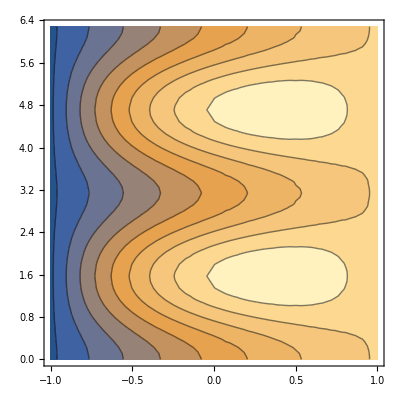

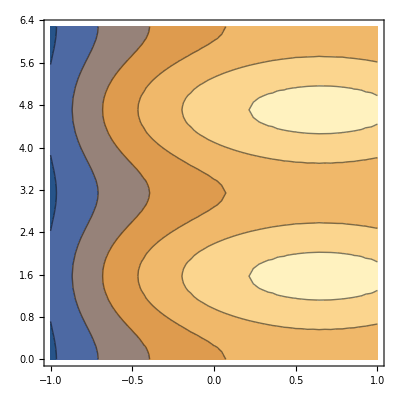

```mathematica
ContourPlot[dΓdcosLdchi[cosL,chi],{cosL, -1, 1},{chi, 0, 2π}]
ContourPlot[dΓdcosLdchiProduct[cosL,chi],{cosL, -1, 1},{chi, 0, 2π}]
```

```mathematica
dΓdcosVdchi[cosV_,chi_]:=NIntegrate[ΓcosLIntegrated[w,cosV,chi,-1,1],{w,wmin,wmax}]
dΓdcosVdchiProduct[cosV_,chi_]:=dΓdcosV[cosV]dΓdchi[chi]*10^15
```

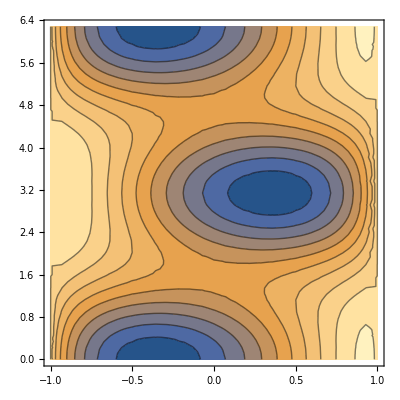

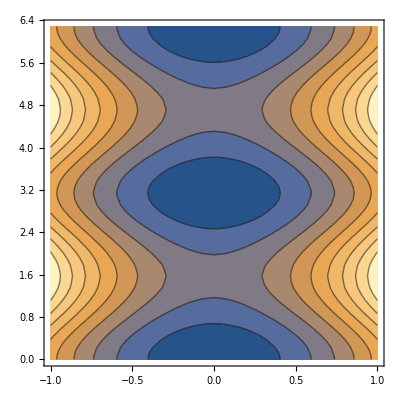

```mathematica
ContourPlot[dΓdcosVdchi[cosV,chi],{cosV, -1, 1},{chi, 0, 2π}]
ContourPlot[dΓdcosVdchiProduct[cosV,chi],{cosV, -1, 1},{chi, 0, 2π}]
```

```mathematica
(* Total Rate *)
```

```mathematica
NIntegrate[ΓcosLcosVchiIntegrated[w,-1, 1,-1,1,0,2π],{w,wmin,wmax}]
```

2.29372×10^-14